```mathematica
multiplicity[volumeRemaining_,tRemaining_,core_]:=Module[{T,V},
T = Length[core]+tRemaining;
V =2*Total[core]+volumeRemaining;



VolumeProfileCount[#]&/@filterMiddle[AllVps[V,T],core]//Total




]
```

```mathematica
11-> 1  2 or 2  1
```

10

```mathematica
AllVps[n,4]
```

Table::iterb: Iterator {i,2,-4+n,2} does not have appropriate bounds.

Table::iterb: Iterator {boundarySize,Table[i,{i,2,-4+n,2}]} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

Table[boundaryPossibilities$261442=Flatten[(Permutations[#1]&)/@IntegerPartitions[boundarySize,{2}],1];bulkPossibilities$261442=Flatten[(Permutations[#1]&)/@IntegerPartitions[(n-boundarySize)/2,{4-2}],1];Table[Table[Join[Join[{bound⟦1⟧},bulk],{bound⟦-1⟧}],{bulk,bulkPossibilities$261442}],{bound,boundaryPossibilities$261442}],{boundarySize,Table[i,{i,2,-4+n,2}]}]

```mathematica
filterMiddle[AllVps[10,4],{1,1}]
```

{2,3}

{{5,1,1,1},{1,1,1,5},{4,1,1,2},{2,1,1,4},{3,1,1,3}}

```mathematica
filterMiddle[list_,core_]:=Module[{start,end},
start = (Length[list[[1]]]-Length[core])/2+1;
end = (Length[list[[1]]]+Length[core])/2;
Select[list,#[[start;;end]]==core&]

]
```

```mathematica
data = Table[multiplicity[V,6,{1,1}],{V,12,22,2}]
```

{1952,17008,113026,640028,3264538,15481116}

```mathematica
model=a*Exp[b*x];

(*Perform the nonlinear fit*)
fit=NonlinearModelFit[data,model,{a,b},x]
```

FittedModel[…]

```mathematica
bestFitModel/.x-> 6
```

1.54835×10^7

{a→1308.71,b→1.56308}

1308.71 ⅇ^(1.56308 x)

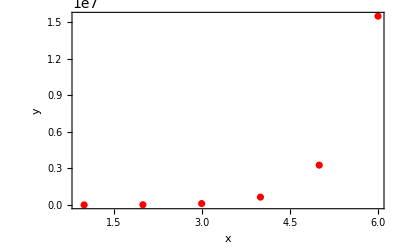

```mathematica
(*Get the best-fit parameters*)bestFitParams=fit["BestFitParameters"]

(*Output the model with the best-fit parameters*)
bestFitModel=model/. bestFitParams

(*Plot the data and the best-fit exponential curve*)
Show[ListPlot[data,PlotStyle->Red,PlotRange->All,Frame->True,FrameLabel->{"x","y","Exponential Fit"}],Plot[bestFitModel,{x,0,24},PlotStyle->Blue]]
```